```mathematica
SetDirectory[NotebookDirectory[]];
matr=Partition[Delete[ReadList["./outputMatrix.txt", Real], 1], 10];
```

```mathematica
(*xArr =Range[1, Length[matr]]/ Length[matr];
data=Thread[{xArr, matr}];*)
```

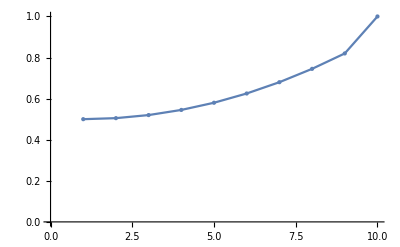

```mathematica
ListPlot[matr[[1]], Joined->True, MeshStyle->PointSize[Medium], Mesh->All]
```